# Add ReLU

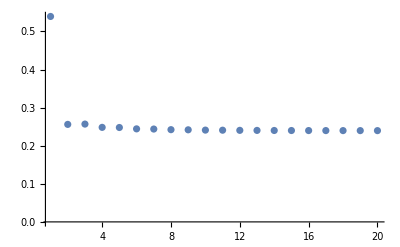

```mathematica
relu[A_]:=MapThread[Max,{Array[0&,Dimensions@A],A},Length[Dimensions[A]]]
reluDot[A_,B_]:=relu[A.B];
errEq:=Y-Fold[reluDot,Reverse[vars]~Join~{makeW[0]}];
lossEq:=take1[1/(2 dsize)errEq.errEqᵀ];

gradEq=D[lossf[Wf],{Wf,1}];
gradf[Wf_]:=gradEq/.subW[Wf];
lossf[Wf_]:=(lossEq/.subW[Wf]/.subY/.subX);

optimizeRegular[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf]
];
];
optimizeRegular[.5,W0f,20];
ListPlot[lossList,PlotRange->All]
```

```mathematica
lossList
```

{0.539407,0.256027,0.25684,0.248212,0.247842,0.244276,0.243793,0.242171,0.241796,0.241016,0.240765,0.240376,0.240219,0.24002,0.239926,0.239822,0.239767,0.239712,0.23968,0.23965}

## Mnist experiments

```mathematica
Export["~/git/whitening/exp/data/relu_losses_regular.csv",lossList];
```

```mathematica
lossList
```

{0.539407,0.256027,0.25684,0.248212,0.247842,0.244276,0.243793,0.242171,0.241796,0.241016}

```mathematica
fs
```

{10,2,2,2,1}

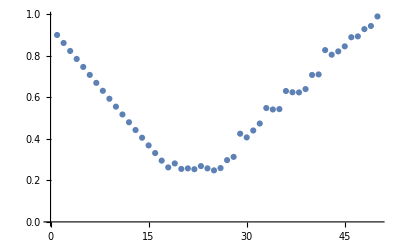

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher2.csv"];
ListPlot@Flatten@data
```

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher3.csv"];
ListPlot@Flatten@data
```

ListPlot[Flatten[$Failed]]

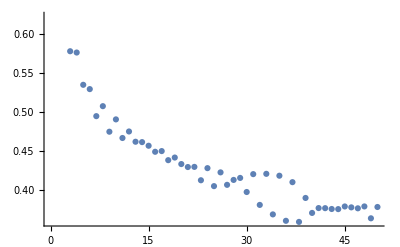

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher3.csv"];
ListPlot@Flatten@data
```

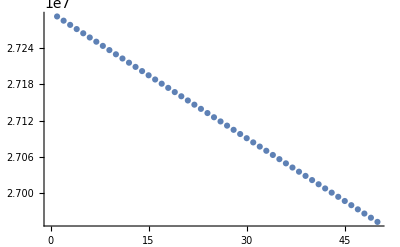

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher4.csv"];
ListPlot@Flatten@data
```

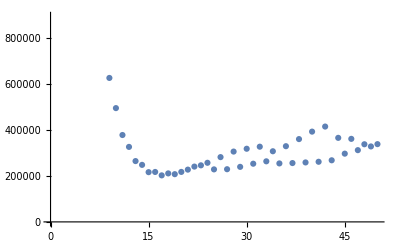

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher4.csv"];
ListPlot@Flatten@data
```

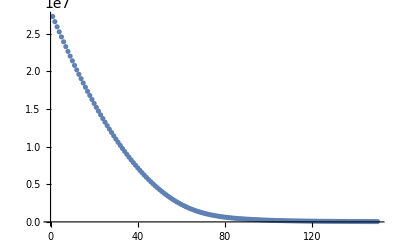

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher4.csv"];
ListPlot@Flatten@data
```

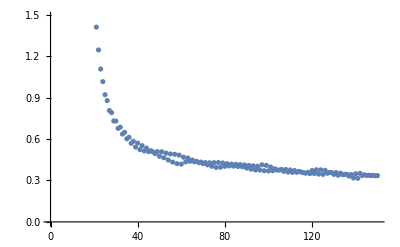

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher4.csv"];
ListPlot@Flatten@data
```

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher6.csv"];
ListPlot@Flatten@data
```

-Graphics-

### 3 mamtuls

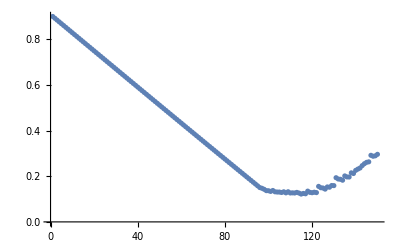

0.12186330140963445856083779972

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher6.csv"];
ListPlot@Flatten@data
Min[data]
```

### 4 matmuls

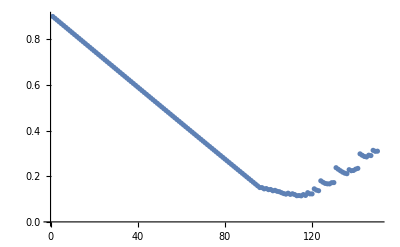

0.11410092784284051048437902409

```mathematica
data=Import["~/git/whitening/exp/data/mnist_fisher7.csv"];
ListPlot@Flatten@data
Min[data]
```